```mathematica
koffa = 3.24*10^-3
kona = 6.29*10^-3
koffp=7.19*10^-3
konp = 7.682*10^-2
na = 2.4*10^5
np = 9.8*10^4
Vcyto = 2.5*10^4
Smem = 4.4*10^3
```

0.00324

0.00629

0.00719

0.07682

240000.

98000.

25000.

4400.

```mathematica
sa = (koffa + kona*Smem/Vcyto)/(kona*na/Vcyto)
sp = (koffp + konp*Smem/Vcyto)/(konp*np/Vcyto)
```

0.0719899

0.0687743

```mathematica
sol = Solve[-s_a*A- K_ap*A*P^alpha +1 == 0 && -s_p*P - K_pa*P*A^beta+1==0,{A,P}]
```

```mathematica
Clear[sa]
Clear[sp]
```

```mathematica
sa = (koffa + kona*Smem/Vcyto)/(kona*na/Vcyto)
sp = (koffp + konp*Smem/Vcyto)/(konp*np/Vcyto)
Manipulate[ContourPlot[{-sa*aa- kap2*aa*pp^alph +1 == 0 , -sp*pp - kpa2*pp*aa^bet+1==0},{aa,-1,20},{pp,-1,20}],{alph,1,5},{bet,1,5},{kap2,10^-5,10^-1},{kpa2,10^-5,10^-1}]
vp=VectorPlot[{f[x,y],g[x,y]},{x,-2,4},{y,-4,2},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{x,y},VectorPoints->16,VectorStyle->{GrayLevel[0.8]}];
```

0.0719899

0.0687743

```mathematica
sa
```

17277.6

```mathematica
Manipluate[
f[aa_,pp_]=-sa*aa- kap2*aa*pp^alph +1;
g[aa_,pp_]=sp*pp - kpa2*pp*aa^bet+1;
vp=VectorPlot[{f[aa,pp],g[aa,pp]},{aa,0,20},{pp,0,20},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{aa,pp},VectorPoints->16,VectorStyle->{GrayLevel[0.8]}];
cp=ContourPlot[{f[aa,pp]==0,g[aa,pp]==0},{aa,0,20},{pp,0,20}];
Show[vp,cp,
Graphics[{Red,PointSize[Large]}]],
{alph,1,5},{bet,1,5},{kap2,10^-10,1},{kpa2,10^-10,1}]
```

Manipluate[-Graphics-,{alph,1,5},{bet,1,5},{kap2,1/10000000000,1},{kpa2,1/10000000000,1}]

```mathematica
ptRules=Solve[{f[aa,pp]==0,g[aa,pp]==0},{aa,pp}];
```

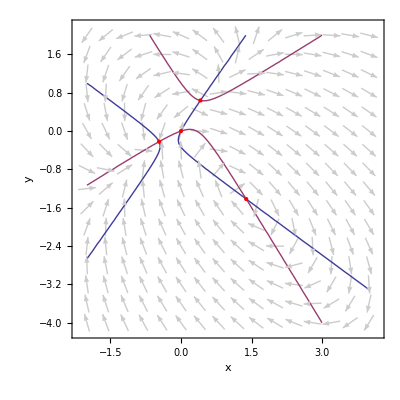

```mathematica
f[x_,y_]=2 x-y+3 (x^2-y^2)+2 x y;
g[x_,y_]=x-3 y-3 (x^2-y^2)+3 x y;
vp=VectorPlot[{f[x,y],g[x,y]},{x,-2,4},{y,-4,2},VectorScale->{0.045,0.9,None},Axes->True,AxesLabel->{x,y},VectorPoints->16,VectorStyle->{GrayLevel[0.8]}];
cp=ContourPlot[{f[x,y]==0,g[x,y]==0},{x,-2,4},{y,-4,2}];
ptRules=NSolve[{f[x,y]==0,g[x,y]==0},{x,y}];
Show[vp,cp,Graphics[{Red,PointSize[Large],Point[{x,y}]/.ptRules}]]
```